# Lab 8: Data Processing -- Carter Colton

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Clear["`*" ]
```

## Assignment 1: Exporting Data

(a) View the xydata array in TableForm to see what it will look like in a file if you use the Table format specifier.
(b) Now Export the xydata array to a file in your working directory named "xydata.txt" using the Table format. (Note that if you were to use a filename with a ".dat" extension, "Table" would be the default format and would not need to be specified.)  View the xydata.txt file to make sure things worked as expected.
(c) Another very common input/output format is the csv or “comma separated variables” format. That format uses comma to separate the data on each line. Mathematica is smart enough that simply by giving the filename a “.csv” extension, it will automatically save the data with commas. Export your xydata array to a file called “xydata.csv” and use a text editor to verify that you now have commas where the xydata.txt file had tabs. (As an added bonus, csv files can typically be opened as spreadsheets in Microsoft Excel by simply double-clicking the file in Windows Explorer.)

```mathematica
SetDirectory[NotebookDirectory[]];
tdata = Import["Th000088.txt","Table"];
```

```mathematica
ourdata=Drop[tdata,1];   (* I've defined "ourdata" so I can refer to it below. It's not needed for this task. *)
Transpose[%];  
Drop[%,-2];
xydata = Transpose[%];
ListLogPlot[xydata] ;
```

```mathematica
TableForm[xydata]
```

171.934 | 0.00549316
172.988 | 0.00610352
174.012 | 0.00579834
175.013 | 0.00701904
176.016 | 0.00793457
177.017 | 0.0076294
178.017 | 0.0076294
179.017 | 0.0076294
180.015 | 0.0088501
181.017 | 0.00793457
182.015 | 0.00915527
183.019 | 0.0088501
184.02 | 0.010376
185.014 | 0.00976563
186.016 | 0.0109863
187.017 | 0.010376
188.016 | 0.0109863
189.016 | 0.0125122
190.016 | 0.0109863
191.016 | 0.0119019
192.016 | 0.012207
193.016 | 0.0125122
194.017 | 0.0128174
195.016 | 0.0131226
196.016 | 0.012207
197.016 | 0.0137329
198.016 | 0.0134277
199.02 | 0.0128174
200.02 | 0.0128174
201.021 | 0.0125122
202.017 | 0.0125122
203.016 | 0.0134277
204.015 | 0.0128174
205.016 | 0.0128174
206.017 | 0.0115967
207.017 | 0.0119019
208.017 | 0.0115967
209.015 | 0.0115967
210.016 | 0.0115967
211.016 | 0.0119019
212.016 | 0.0100708
213.016 | 0.0100708
214.017 | 0.0088501
215.016 | 0.00976563
216.017 | 0.0100708
217.014 | 0.00854492
218.017 | 0.00915527
219.015 | 0.00732422
220.016 | 0.00793457
221.017 | 0.00671387
222.016 | 0.00732422
223.016 | 0.00732422
224.016 | 0.00640869
225.017 | 0.00610352
226.018 | 0.00701904
227.015 | 0.00518799
228.016 | 0.00610352
229.015 | 0.00518799
230.016 | 0.00610352
231.017 | 0.00488281
232.016 | 0.00488281
233.016 | 0.00457764
234.015 | 0.00366211
235.016 | 0.00549316
236.019 | 0.00366211
237.019 | 0.00488281
238.017 | 0.00457764
239.016 | 0.00396729
240.016 | 0.00427246
241.015 | 0.00366211
242.015 | 0.00244141
243.016 | 0.00366211
244.018 | 0.00244141
245.015 | 0.00366211
246.016 | 0.00335693
247.016 | 0.00427246
248.016 | 0.00274658
249.02 | 0.00305176
250.02 | 0.00335693

```mathematica
Export["xydata.txt",xydata,"Table"]
```

xydata.txt

```mathematica
Export["xydata.csv",xydata, "Table"]
```

xydata.csv

## Assignment 2: A String Function

Create a function using Module which takes two arguments: an expression containing x and a numerical value to plug in for x, then prints out the phrase “The value of <expression> when x = <number> is: <the answer>”.

```mathematica
stringfunction[expression_,number_]:=Module[{newfunction,evaluated},
evaluated = expression/.x->number;
newfunction[x_]:=expression[x];
sentence1="The value of " <>ToString[expression]<>" when x = "<>ToString[number]<>" is: " <>ToString[evaluated];
sentence1
]
```

```mathematica
stringfunction[2*x,2]
```

The value of 2 x when x = 2 is: 4

## Assignment 3: Black and White Peppers

The goal of this problem is to produce a black and white peppers image based on the color image of the peppers seen above. Part (a) is an easier version of the problem, then part (b) applies the same technique to the peppers image itself. 

(a) Working with your colorarray data from above, figure out how to replace each pixel, i.e. each three element list, with a single number that is the average of the three values. Use the Map command, which we often shortcut as  /@.  

Hint: You cannot actually easily use the shortcut notation in this case, because the default behavior of Map (and  /@ ) is to perform an operation on each row of the matrix. We need to perform an operation (i.e. average the numbers) on each pixel in the matrix. Using Map with a  {2}  for the “levelspec” argument will do this. (Look at the help file to see where that goes.) You will know that you have succeeded when you can view the result in MatrixForm, and see a 20x10 list of numbers (rather than a 20x10 list of triplets).  And when you have done that, you will be able to use Image to see a black and white version of your colorarray data.

(b) Now use the same technique on colorpeppersdata. This creates a black and white equivalent of the original color image of the peppers. View it with Image to verify the result, then Export the grayscale image to a “.jpg” file and open that file with external software.

```mathematica
colorarray=RandomReal[{0,1},{20,10,3}];  (* a 20x10 array of pixels, each pixel now being a 3 element list *)
colorarray//MatrixForm;
```

```mathematica
mapimage = Map[Mean,colorarray,{2}];
Image[mapimage]
```

-Graphics-

```mathematica
colorpeppers = ExampleData[{"TestImage","Peppers"}];
```

```mathematica
colorpeppers//InputForm;
```

```mathematica
colorpeppersdata = colorpeppers//ImageData; 
colorpeppersdata//MatrixForm;
mapimagepeppers = Map[Mean,colorpeppersdata,{2}];
Image[mapimagepeppers]
```

-Graphics-

```mathematica
Export["colorlesspeppers.jpg",%]
```

colorlesspeppers.jpg

## Assignment 4: Exporting an Animation

Export an animated gif (save it to the notebook directory as “filename.gif”) of the function f(x,y,t)=3 cos(0.2 t) exp(-1/3 (x^2+y^2)) for x and y between -5 and 5, and t going from 0 to 20π (in steps of 0.5). Use Plot3D to display the function. Use PlotRange->{All, All, {-3,3}}  as a plot option in order to preserve the z-axis scale from plot to plot.

```mathematica
f[x_,y_,t_]=3 cos(0.2 t) exp(-1/3 (x^2+y^2))
```

3 ⅇ^(1/3 (-x^2-y^2)) Cos[0.2 t]

```mathematica
table = Table[Plot3D[f[x,y,t],{x,-5,5},{y,-5,5},PlotRange->{All,All,{-3,3}},PlotPoints->50],{t,0,20*Pi,0.5}];
```

```mathematica
Export["filename.gif",table,AnimationRate->10]
```

filename.gif

## Assignment 5: Deepening a French Horn

(a) Find and load the FrenchHorn example data listed under “Sound”. Play the sound (the Play command is not even needed). Use InputForm to look at the metadata at the end of the list of numbers (delete after done viewing). There should be only a single item of metadata: the number 22050. That indicates the sampling rate (in Hz). It’s at the [[1,2]] position of the data, as you should be able to verify.
(b) Modify the horn sound by replacing the number 22050 with the number 11025. What happens to the horn sound, and why? (There are two effects.) 
(c) Export the new sound as a wav file, and verify that it plays in e.g. Windows Media Player.

```mathematica
ExampleData["Sound"]
```

{{Sound,AltoFlute},{Sound,AltoFluteScale},{Sound,AltoSaxophone},{Sound,AltoSaxophoneScale},{Sound,Apollo11PhoneCall},{Sound,Apollo11ReturnSafely},{Sound,Apollo11SmallStep},{Sound,Apollo13Countdown},{Sound,Apollo13Problem},{Sound,BalloonPop},{Sound,BassClarinet},{Sound,BassClarinetScale},{Sound,BassFlute},{Sound,BassFluteScale},{Sound,Bassoon},{Sound,BassoonScale},{Sound,BassTrombone},{Sound,BassTromboneScale},{Sound,BlackcapWarbler},{Sound,Burst100},{Sound,Burst1000},{Sound,Burst7350},{Sound,Cello},{Sound,CelloPizzicato},{Sound,CelloPizzicatoScale},{Sound,CelloScale},{Sound,Clarinet},{Sound,ClarinetScale},{Sound,CrashCymbal},{Sound,DoubleBass},{Sound,DoubleBassPizzicato},{Sound,DoubleBassPizzicatoScale},{Sound,DoubleBassScale},{Sound,Flute},{Sound,FluteScale},{Sound,FrenchHorn},{Sound,FrenchHornScale},{Sound,JetSound},{Sound,LinearSweep},{Sound,NoiseBlue},{Sound,NoiseBrown},{Sound,NoisePink},{Sound,NoiseViolet},{Sound,NoiseWhite},{Sound,Oboe},{Sound,OboeScale},{Sound,OrganChord},{Sound,Piano},{Sound,PianoScale},{Sound,RollingCoin},{Sound,SopranoSaxophone},{Sound,SopranoSaxophoneScale},{Sound,Square10},{Sound,Square100},{Sound,Square1000},{Sound,Square7350},{Sound,SubwayTrain},{Sound,TenorTrombone},{Sound,TenorTromboneScale},{Sound,TestIntermodulationDistortion},{Sound,Trumpet},{Sound,TrumpetScale},{Sound,Tuba},{Sound,TubaScale},{Sound,Viola},{Sound,ViolaScale},{Sound,Violin},{Sound,ViolinScale}}

```mathematica
frenchhorn=ExampleData[{"Sound","FrenchHorn"}]
```

-Graphics-

```mathematica
frenchhorn//InputForm;
```

```mathematica
frenchhorn[[1,2]]
frenchhorn[[1,2]]=11025;
frenchhorn[[1,2]]
```

22050

11025

```mathematica
frenchhorn
```

-Graphics-

The horn sound gets deeper and it also plays for double the amount of time.

```mathematica
Export["frenchhorn.wav",frenchhorn]
```

frenchhorn.wav

## Assignment 6: Melting and Boiling Points

(a) Create a 2D list that contains a pair of Kelvin-degree temperatures, the "AbsoluteMeltingPoint" and the "AbsoluteBoilingPoint", for each element in the database. (No need to have the element name in the list.) Then use skipmissing to eliminate the pairs that are Missing one or both of these temperatures, and employ N to ensure that all of the entries contain true floating-point data.
(b) ListPlot the resulting data with the following options:  PlotRange → All, Frame → True, FrameLabel → {“Melting Point (K)”, “Boiling Point (K)”}.  What do you learn from this plot?

```mathematica
skipmissing[data_] := Select[data,!MemberQ[Flatten[#],_Missing]&]
```

```mathematica
elementdata ={ ElementData[#, "AbsoluteMeltingPoint"], ElementData[#,"AbsoluteBoilingPoint"]}&/@ElementData[];
plotthedata = elementdata//skipmissing//N
```

{{14.01 K,20.28 K},{453.69 K,1615. K},{1560. K,2743. K},{2348. K,4273. K},{3823. K,4300. K},{63.05 K,77.36 K},{54.8 K,90.2 K},{53.5 K,85.03 K},{24.56 K,27.07 K},{370.87 K,1156. K},{923. K,1363. K},{933.47 K,2792. K},{1687. K,3173. K},{317.3 K,553.6 K},{388.36 K,717.87 K},{171.6 K,239.11 K},{83.8 K,87.3 K},{336.53 K,1032. K},{1115. K,1757. K},{1814. K,3103. K},{1941. K,3560. K},{2183. K,3680. K},{2180. K,2944. K},{1519. K,2334. K},{1811. K,3134. K},{1768. K,3200. K},{1728. K,3186. K},{1357.77 K,2835. K},{692.68 K,1180. K},{302.91 K,2477. K},{1211.4 K,3093. K},{1090. K,887. K},{494. K,958. K},{265.8 K,332. K},{115.79 K,119.93 K},{312.46 K,961. K},{1050. K,1655. K},{1799. K,3618. K},{2128. K,4682. K},{2750. K,5017. K},{2896. K,4912. K},{2430. K,4538. K},{2607. K,4423. K},{2237. K,3968. K},{1828.05 K,3236. K},{1234.93 K,2435. K},{594.22 K,1040. K},{429.75 K,2345. K},{505.08 K,2875. K},{903.78 K,1860. K},{722.66 K,1261. K},{386.85 K,457.4 K},{161.3 K,165.1 K},{301.59 K,944. K},{1000. K,2143. K},{1193. K,3737. K},{1071. K,3633. K},{1204. K,3563. K},{1294. K,3373. K},{1373. K,3273. K},{1345. K,2076. K},{1095. K,1800. K},{1586. K,3523. K},{1629. K,3503. K},{1685. K,2840. K},{1747. K,2973. K},{1770. K,3141. K},{1818. K,2223. K},{1092. K,1469. K},{1936. K,3675. K},{2506. K,4876. K},{3290. K,5731. K},{3695. K,5828. K},{3459. K,5869. K},{3306. K,5285. K},{2739. K,4701. K},{2041.4 K,4098. K},{1337.33 K,3129. K},{234.32 K,629.88 K},{577. K,1746. K},{600.61 K,2022. K},{544.4 K,1837. K},{528. K,1235. K},{202. K,211.3 K},{973. K,2010. K},{1323. K,3473. K},{2023. K,5093. K},{1845. K,4273. K},{1408. K,4200. K},{917. K,4273. K},{913. K,3503. K},{1449. K,2284. K},{1618. K,3383. K}}

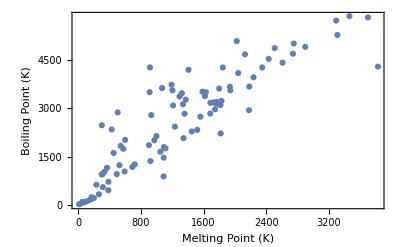

```mathematica
ListPlot[plotthedata,PlotRange->All,Frame->True,FrameLabel->{"Melting Point (K)", "Boiling Point (K)"}]
```

I learn that as the atomic number of the element gets bigger, so does the melting and boiling points, for the most part.

## Assignment 7: Hubble’s Law

(a) Create a 2D list called data1 that contains pairs of numbers: the “DistanceLightYears” and the “Redshift”, for every "Galaxy" in the AstronomicalData database (supress the output; it’s long).  Then use skipmissing to eliminate the pairs that are Missing one or both of these quantities, and employ N to ensure that all of the entries contain true floating-point data.  Name the result data1.  Once you have succeeded, suppress the lengthy output with a semicolon. Hint: Be sure to select for galaxies the same way I selected for planets in the example above. To check yourself, there were 729 useable galaxies in the curated data as of Jan 2014.

(b) The distances in data1 are measured in light years and the redshifts are unitless.  A more traditional description would express the distances in megaparsecs, and would multiply the unitless redshifts by the speed of light in kilometers per second.  We provide multiplicative conversion factors in the cell below.  Convert data1 to traditional units and name the result data2. Then ListPlot data2. You should find a nearly linear relationship between how far away a galaxy is (the x-axis, the distance in megaparsecs), and how fast it’s traveling (the y-axis, the redshift in km/s). That is Hubble’s Law, discovered by Edwin Hubble in 1929, and is strong evidence for the Big Bang theory (the scientific model, not the TV show). The slope of the line indicates the rate of the expansion of the universe. 

Hint: One way to apply the conversion factors is to make a nameless function that multiplies the first element of a pair by mpperly and the 2nd element of a pair by lightspeed, and then use /@ to evaluate this function for each element in data1. Alternatively, you could separate data1 into two lists with Transpose, multiply each list by the appropriate constant, then re-form your x-y pairs with a second Transpose command.

```mathematica
skipmissing[data_] := Select[data,!MemberQ[Flatten[#],_Missing]&]
```

```mathematica
astronomicaldata ={ AstronomicalData[#, "DistanceLightYears"], AstronomicalData[#,"Redshift"]}&/@AstronomicalData["Galaxy"];
data1 = astronomicaldata//skipmissing//N;
```

```mathematica
mpperly = 3.0660*^-7; (* Megaparsecs/LightYear *)
lightspeed = 2.9979*10^5; (* km/sec *)
```

```mathematica
data2 = {#[[1]]*mpperly,#[[2]]*lightspeed}&/@data1;
```

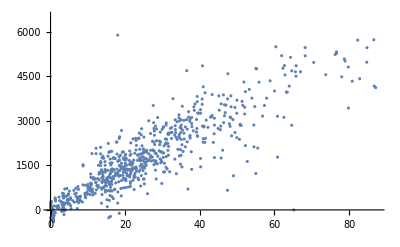

```mathematica
ListPlot[data2]
```

```mathematica
f[x_]={x*mpperly,x*lightspeed};
f/@data1; (*this is just for me to remember an alternate way to do it*)
```

## Assignment 8: Calculating Spin Resonance Data

(a) The file spinres.csv, available on the Physics 230 website, contains data from an electron spin resonance experiment I did where the magnetic field was changed while we recorded an optical signal measuring electron spin polarization. The first column represents the magnetic field as recorded by a magnetic field sensor; the second column is the optical signal. Read in the file and ListPlot the data. Be sure to use the PlotRange->All option. Hint: since it’s in a nice csv format, you can read the data in with a simple Import comand without any options.
(b) The y-axis scale isn’t too important, but the x-axis scale is critical. The problem here is that the x-axis is not really displaying magnetic field (which should range from 0.718 to 0.841 T), it’s displaying the voltage from my field sensor (which ranged from -1.207 to -1.157 V). We need to therefore convert the magnetic field sensor data into tesla and replot. In a separate experiment, I calibrated the magnetic field sensor so I would know what voltage from the sensor corresponded to what field. The calibration information is in in a file called calibration.csv; the first column is voltage and the second column is the field (in tesla) that a given voltage corresponded to. Read in the calibration information, use it to define a calibrating function (via Interpolation), and use that to change your x-values into tesla. Then make a ListPlot of the optical signal vs. actual field in tesla. This plot should look like a reversed version of the first plot, but with the proper magnetic field range (0.718 - 0.841 T) along the x-axis.

```mathematica
spindata = Import["spinres.csv"];
newspindata=Drop[spindata,1]
```

{{-1.15707,0.03255},{-1.15771,-0.00498},{-1.15823,-0.00277},{-1.15867,0.02703},{-1.15907,0.0469},{-1.15951,0.03144},{-1.16003,0.00385},{-1.16067,0.02813},{-1.16176,0.03144},{-1.16228,0.02593},{-1.16305,0.02151},{-1.16378,-0.00609},{-1.16435,0.00164},{-1.16467,0.01378},{-1.16508,0.01047},{-1.16565,-0.00167},{-1.16605,0.00606},{-1.16671,0.00826},{-1.16781,0.00164},{-1.16835,0.00826},{-1.16913,0.01268},{-1.16975,0.01489},{-1.17041,-0.00277},{-1.17087,0.00606},{-1.17135,0.01268},{-1.17194,-0.00277},{-1.17244,-0.00498},{-1.17316,0.02041},{-1.17421,0.01047},{-1.17485,0.04248},{-1.17581,0.02813},{-1.1764,0.05904},{-1.17714,0.08001},{-1.17764,0.08553},{-1.17824,0.08332},{-1.17874,0.11754},{-1.1792,0.17052},{-1.17993,0.3085},{-1.18116,0.74118},{-1.18189,1.00168},{-1.1827,0.92111},{-1.18343,0.65178},{-1.18415,0.43874},{-1.18464,0.33278},{-1.18522,0.26655},{-1.18571,0.20474},{-1.18615,0.12968},{-1.18685,0.08663},{-1.18803,0.05352},{-1.1886,0.048},{-1.18929,0.01489},{-1.18997,-0.000567},{-1.19065,0.02041},{-1.19111,0.01268},{-1.19178,0.02593},{-1.19218,0.03255},{-1.19271,0.03034},{-1.19319,0.000537},{-1.19415,0.01047},{-1.19467,0.01268},{-1.19526,-0.000567},{-1.19563,0.02151},{-1.19621,0.02151},{-1.19679,0.02041},{-1.19726,0.01599},{-1.19766,0.01158},{-1.19806,0.0182},{-1.19842,0.02813},{-1.19893,0.02041},{-1.19986,-0.00277},{-1.20025,-0.02927},{-1.20119,-0.03478},{-1.20176,-0.01492},{-1.20226,-0.01823},{-1.20262,-0.01933},{-1.20301,-0.0105},{-1.20337,0.00606},{-1.20376,-0.01823},{-1.20433,0.00164},{-1.20529,-0.01271},{-1.20576,-0.00719},{-1.20662,-0.0105},{-1.20709,-0.00609}}

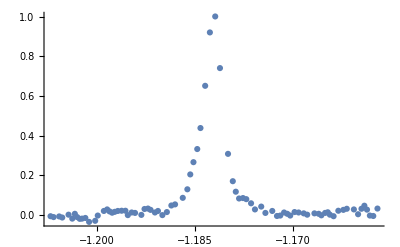

```mathematica
ListPlot[%,PlotRange->All]
```

```mathematica
calibration = Import["calibration.csv"];
calibrationdrop = Drop[calibration,1]
```

{{-0.925,0.096},{-0.932,0.1165},{-0.939,0.137},{-0.946,0.157},{-0.953,0.177},{-0.96,0.198},{-0.968,0.218},{-0.975,0.2385},{-0.982,0.259},{-0.989,0.278},{-0.998,0.306},{-1.0175,0.357},{-1.0368,0.409},{-1.0568,0.459},{-1.075,0.51},{-1.094,0.559},{-1.113,0.607},{-1.132,0.656},{-1.152,0.705},{-1.171,0.752},{-1.192,0.799},{-1.209,0.846},{-1.228,0.894},{-1.248,0.941}}

```mathematica
calibrationfunction = Interpolation[calibrationdrop]
```

InterpolatingFunction[…]

```mathematica
plotcalibrationfunction={calibrationfunction[#[[1]]],#[[2]]}&/@newspindata
```

{{0.71768,0.03255},{0.71928,-0.00498},{0.72058,-0.00277},{0.72168,0.02703},{0.72268,0.0469},{0.72378,0.03144},{0.72508,0.00385},{0.72668,0.02813},{0.72938,0.03144},{0.73068,0.02593},{0.73258,0.02151},{0.73438,-0.00609},{0.73578,0.00164},{0.73658,0.01378},{0.73758,0.01047},{0.73898,-0.00167},{0.73998,0.00606},{0.74158,0.00826},{0.74428,0.00164},{0.74558,0.00826},{0.74748,0.01268},{0.74898,0.01489},{0.75058,-0.00277},{0.75168,0.00606},{0.75278,0.01268},{0.75408,-0.00277},{0.75518,-0.00498},{0.75678,0.02041},{0.75908,0.01047},{0.76048,0.04248},{0.76258,0.02813},{0.76388,0.05904},{0.76548,0.08001},{0.76658,0.08553},{0.76788,0.08332},{0.76898,0.11754},{0.76998,0.17052},{0.77158,0.3085},{0.77428,0.74118},{0.77588,1.00168},{0.77768,0.92111},{0.77928,0.65178},{0.78088,0.43874},{0.78198,0.33278},{0.78328,0.26655},{0.78438,0.20474},{0.78538,0.12968},{0.78698,0.08663},{0.78968,0.05352},{0.79098,0.048},{0.79258,0.01489},{0.79418,-0.000567},{0.79578,0.02041},{0.79688,0.01268},{0.79848,0.02593},{0.79948,0.03255},{0.80088,0.03034},{0.80218,0.000537},{0.80478,0.01047},{0.80618,0.01268},{0.80778,-0.000567},{0.80878,0.02151},{0.81038,0.02151},{0.81198,0.02041},{0.81328,0.01599},{0.81438,0.01158},{0.81548,0.0182},{0.81648,0.02813},{0.81788,0.02041},{0.82048,-0.00277},{0.82158,-0.02927},{0.82418,-0.03478},{0.82578,-0.01492},{0.82718,-0.01823},{0.82818,-0.01933},{0.82928,-0.0105},{0.83028,0.00606},{0.83138,-0.01823},{0.83298,0.00164},{0.83568,-0.01271},{0.83698,-0.00719},{0.83938,-0.0105},{0.84068,-0.00609}}

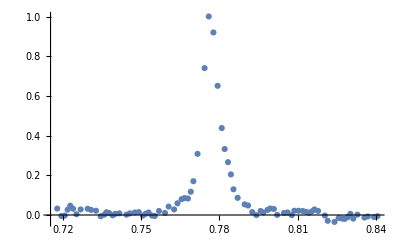

```mathematica
ListPlot[plotcalibrationfunction,PlotRange->All]
```